```mathematica
(*mathematica*)
```

```mathematica
(*graph matric tetrahedron projection HyperFuchsian triangle group:<p,q,r>*)
```

```mathematica
Clear[s,p,q,r,s]
```

```mathematica
s=s/.Solve[1/p+1/q+1/r+1/s-1==0,s][[1]]
```

(p q r)/(-p q-p r-q r+p q r)

```mathematica
gm={{0,p,1,0},
{0,0,q,0},
{0,0,0,r},
{s,1,0,1}}
```

{{0,p,1,0},{0,0,q,0},{0,0,0,r},{(p q r)/(-p q-p r-q r+p q r),1,0,1}}

```mathematica
gmm=gm.Transpose[gm]
```

{{1+p^2,q,0,p},{q,q^2,0,0},{0,0,r^2,r},{p,0,r,2+(p^2 q^2 r^2)/(-p q-p r-q r+p q r)^2}}

```mathematica
Reduce[Det[gmm]==1,{p,q,r}]
```

(p q≠0&&(r==(-p-q+p q-√(-4 p^3 q^3+(p+q-p q)^2))/(2 p^2 q^2)||r==(-p-q+p q+√(-4 p^3 q^3+(p+q-p q)^2))/(2 p^2 q^2)))||(p q≠0&&(r==(p+q-p q-√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2)||r==(p+q-p q+√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2)))

```mathematica
N[(p q≠0&&(r==(-p-q+p q-√(-4 p^3 q^3+(p+q-p q)^2))/(2 p^2 q^2)||r==(-p-q+p q+√(-4 p^3 q^3+(p+q-p q)^2))/(2 p^2 q^2)))||(p q≠0&&(r==(p+q-p q-√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2)||r==(p+q-p q+√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2)))/.p->2/.q->3]
```

r==0.0138889-0.408012 ⅈ||r==0.0138889+0.408012 ⅈ||r==-0.422373||r==0.394596

```mathematica
ExpandAll[(r-(0.013888888888888888-0.40801196726578837 ⅈ))*(r-(0.013888888888888888+0.40801196726578837 ⅈ))*(r+0.4223733658292428)*(r-0.39459558805146505)]//Chop
```

-0.0277778+0.00925926 r-0.000771605 r^2+r^4

```mathematica
Det[gm]
```

-(p^2 q^2 r^2)/(-p q-p r-q r+p q r)

```mathematica
Reduce[-(p^2 q^2 r^2)/(-p q-p r-q r+p q r)==1,{p,q,r}]
```

p q≠0&&(r==(p+q-p q-√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2)||r==(p+q-p q+√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2))

```mathematica
ExpandAll[CharacteristicPolynomial[gm,x]]
```

-(p^2 q^2 r^2)/(-p q-p r-q r+p q r)-q r x-(p q r^2 x)/(-p q-p r-q r+p q r)-x^3+x^4

```mathematica
Table[-(p^2 q^2 r^2)/(-p q-p r-q r+p q r)-q r x-(p q r^2 x)/(-p q-p r-q r+p q r)-x^3+x^4/.p->2/.q->3,{r,3,7}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression -18 x-x^3+x^4+ComplexInfinity+ComplexInfinity encountered.

{108+9 x-x^3+x^4,288+36 x-x^3+x^4,900+135 x-x^3+x^4,Indeterminate,-1764-315 x-x^3+x^4}

```mathematica
px={108+9 x-x^3+x^4,288+36 x-x^3+x^4,900+135 x-x^3+x^4,-1764-315 x-x^3+x^4}
```

{108+9 x-x^3+x^4,288+36 x-x^3+x^4,900+135 x-x^3+x^4,-1764-315 x-x^3+x^4}

```mathematica
Table[x/.NSolve[px[[i]]==0,x],{i,4}]
```

{{-2.06631-2.05424 ⅈ,-2.06631+2.05424 ⅈ,2.56631-2.47703 ⅈ,2.56631+2.47703 ⅈ},{-2.72345-2.37437 ⅈ,-2.72345+2.37437 ⅈ,3.22345-3.41617 ⅈ,3.22345+3.41617 ⅈ},{-3.74311-2.7043 ⅈ,-3.74311+2.7043 ⅈ,4.24311-4.91952 ⅈ,4.24311+4.91952 ⅈ},{-4.28268,-1.56515-6.81978 ⅈ,-1.56515+6.81978 ⅈ,8.41297}}

```mathematica
Table[WeightedAdjacencyGraph[gm/.p->2/.q->3,PlotTheme->"ClassicDiagram"],{r,3,7}]
```

Power::infy: Infinite expression 1/0 encountered.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pr=Union[Flatten[Table[Table[p/.NSolve[(p+q-p q+√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2)==i,p],{i,10}],{q,10}]]]
```

{-0.59307,-0.524461,-0.5,-0.469726,-0.427661,-0.422373,-0.394596,-0.369523,-0.367898,-0.352366,-0.345827,-0.331583,-0.327218,-0.311267,-0.306558,-0.302898,-0.280321,-0.274223,-0.266113,-0.261993,-0.25,-0.246752,-0.237779,-0.23383,-0.231046,-0.216638,-0.215721,-0.21236,-0.203013,-0.200135,-0.193435,-0.192263,-0.186812,-0.178679,-0.176183,-0.175776,-0.166776,-0.166448,-0.162742,-0.156922,-0.151905,-0.150332,-0.148594,-0.142934,-0.140327,-0.135355,-0.132048,-0.130997,-0.125053,-0.123275,-0.116752,-0.116016,-0.109883,-0.10408,0.09608,0.101118,0.106414,0.107065,0.112666,0.114237,0.119278,0.120206,0.123133,0.127253,0.12956,0.134594,0.135754,0.137148,0.141613,0.146302,0.149901,0.150198,0.157664,0.158029,0.159904,0.167281,0.172324,0.173374,0.178451,0.182437,0.18836,0.192333,0.193151,0.206102,0.210279,0.21383,0.222222,0.225147,0.234863,0.238556,0.243111,0.25481,0.271836,0.27512,0.301583,0.315329,0.321267,0.338273,0.339563,0.361452,0.388306,0.394596,0.422373,0.467661,0.5,0.532226,0.635573,0.84307,1.61803}

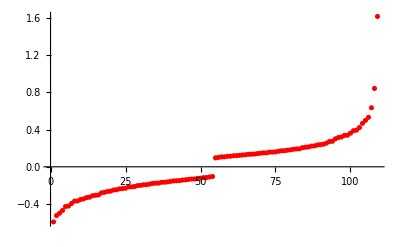

```mathematica
ListPlot[pr,PlotStyle->Red,PlotRange->All]
```

```mathematica
Table[(p+q-p q+√(4 p^3 q^3+(-p-q+p q)^2))/(2 p^2 q^2)/.p->N[GoldenRatio],{q,-10,10}]
```

Power::infy: Infinite expression 1/0 encountered.

{0.0148936+0.248156 ⅈ,0.0169299+0.261503 ⅈ,0.0195826+0.277256 ⅈ,0.0231685+0.296233 ⅈ,0.0282561+0.319699 ⅈ,0.0359675+0.349733 ⅈ,0.0488221+0.390032 ⅈ,0.0736799+0.447864 ⅈ,0.136271+0.538931 ⅈ,0.427051+0.660047 ⅈ,ComplexInfinity,1.,0.574429,0.448903,0.383013,0.340511,0.310048,0.286769,0.268198,0.252916,0.240042}

```mathematica
(*end*)
```